```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Automatic ROLO algorithm
```

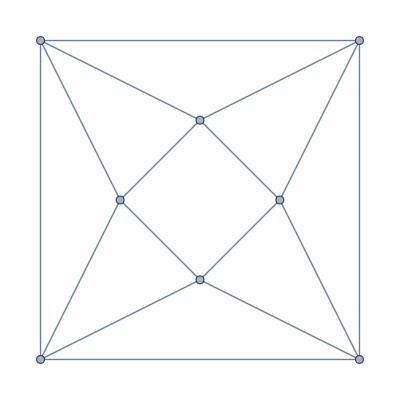

{{0,1,0,1,1,0,0,1},{1,0,1,0,1,1,0,0},{0,1,0,1,0,1,1,0},{1,0,1,0,0,0,1,1},{1,1,0,0,0,1,0,1},{0,1,1,0,1,0,1,0},{0,0,1,1,0,1,0,1},{1,0,0,1,1,0,1,0}}

-Graphics-

```mathematica
(*dim=8;
vertices = 20;
Gin = Import["C:\\Users\\Alberto\\Desktop\\ROLOfieles_OFFLINE\\Resolutor ROLO\\fully205k8.g6"]
AMG=Import["C:\\Users\\Alberto\\Desktop\\ROLOfieles_OFFLINE\\Resolutor ROLO\\fully205k8.g6","AdjacencyMatrix"];
AM = AMG[[1]];
G=Gin[[1]]*)
dim=3;
vertices=8;
Gin=GraphData[{"Circulant",{8,{1,2}}}]
AMG=AdjacencyMatrix[%];
AM=Normal[%]
G=Gin
```

```mathematica
clique=FindClique[G,8]
```

{{1,2,5}}

```mathematica
lista=Array[Subscript[x, ##]&,{vertices,dim}];
Do[lista=lista/.Subscript[x, clique[[1,k]],k]->1/.Subscript[x, clique[[1,k]],y_]:>0,{k,1,Length[clique[[1]]]}];
lista2=Array[Subscript[xi, ##]&,{vertices,dim}];
Do[lista2=lista2/.Subscript[xi, clique[[1,k]],k]->0/.Subscript[xi, clique[[1,k]],y_]:>0,{k,1,Length[clique[[1]]]}];
X=lista (* VALORES REALES DE X *)
XI = lista2  (* VALORES COMPLEJOS DE X *)
```

{{1,0,0},{0,1,0},{x_(3,1),x_(3,2),x_(3,3)},{x_(4,1),x_(4,2),x_(4,3)},{0,0,1},{x_(6,1),x_(6,2),x_(6,3)},{x_(7,1),x_(7,2),x_(7,3)},{x_(8,1),x_(8,2),x_(8,3)}}

{{0,0,0},{0,0,0},{xi_(3,1),xi_(3,2),xi_(3,3)},{xi_(4,1),xi_(4,2),xi_(4,3)},{0,0,0},{xi_(6,1),xi_(6,2),xi_(6,3)},{xi_(7,1),xi_(7,2),xi_(7,3)},{xi_(8,1),xi_(8,2),xi_(8,3)}}

```mathematica
Prov={}; (* RESTRICCION DE ORTOGONALIDAD EN ADYACENCIA  *)
Do[If[AM[[i,j]]==1,Prov=Append[Prov,Sum[X[[i,k]]*X[[j,k]]-XI[[i,k]]*XI[[j,k]],{k,1,dim}]*Sum[X[[i,k]]*XI[[j,k]]+X[[j,k]]*XI[[i,k]],{k,1,dim}]==0]],{i,1,vertices-1},{j,i+1,vertices}];
Prov
Prov2={}; (* RESTRICCION DE NO ORTOGONALIDAD EN NO ADYACENCIA  *)
Do[If[AM[[i,j]]==0,Prov2=Append[Prov2,Sum[X[[i,k]]*X[[j,k]]-XI[[i,k]]*XI[[j,k]],{k,1,dim}]+Sum[X[[i,k]]*XI[[j,k]]+X[[j,k]]*XI[[i,k]],{k,1,dim}]!=0]],{i,1,vertices-1},{j,i+1,vertices}];
Prov2
Prov3={}; (* RESTRICCION MODULO 1 *)
Do[ Prov3=Append[Prov3,Sum[X[[i,j]]*X[[i,j]]+XI[[i,j]]*XI[[i,j]],{j,1,dim}]==1],{i,1,vertices}];
Prov3
```

{True,x_(4,1) xi_(4,1)==0,True,x_(8,1) xi_(8,1)==0,x_(3,2) xi_(3,2)==0,True,x_(6,2) xi_(6,2)==0,(x_(4,1) xi_(3,1)+x_(4,2) xi_(3,2)+x_(4,3) xi_(3,3)+x_(3,1) xi_(4,1)+x_(3,2) xi_(4,2)+x_(3,3) xi_(4,3)) (x_(3,1) x_(4,1)+x_(3,2) x_(4,2)+x_(3,3) x_(4,3)-xi_(3,1) xi_(4,1)-xi_(3,2) xi_(4,2)-xi_(3,3) xi_(4,3))==0,(x_(6,1) xi_(3,1)+x_(6,2) xi_(3,2)+x_(6,3) xi_(3,3)+x_(3,1) xi_(6,1)+x_(3,2) xi_(6,2)+x_(3,3) xi_(6,3)) (x_(3,1) x_(6,1)+x_(3,2) x_(6,2)+x_(3,3) x_(6,3)-xi_(3,1) xi_(6,1)-xi_(3,2) xi_(6,2)-xi_(3,3) xi_(6,3))==0,(x_(7,1) xi_(3,1)+x_(7,2) xi_(3,2)+x_(7,3) xi_(3,3)+x_(3,1) xi_(7,1)+x_(3,2) xi_(7,2)+x_(3,3) xi_(7,3)) (x_(3,1) x_(7,1)+x_(3,2) x_(7,2)+x_(3,3) x_(7,3)-xi_(3,1) xi_(7,1)-xi_(3,2) xi_(7,2)-xi_(3,3) xi_(7,3))==0,(x_(7,1) xi_(4,1)+x_(7,2) xi_(4,2)+x_(7,3) xi_(4,3)+x_(4,1) xi_(7,1)+x_(4,2) xi_(7,2)+x_(4,3) xi_(7,3)) (x_(4,1) x_(7,1)+x_(4,2) x_(7,2)+x_(4,3) x_(7,3)-xi_(4,1) xi_(7,1)-xi_(4,2) xi_(7,2)-xi_(4,3) xi_(7,3))==0,(x_(8,1) xi_(4,1)+x_(8,2) xi_(4,2)+x_(8,3) xi_(4,3)+x_(4,1) xi_(8,1)+x_(4,2) xi_(8,2)+x_(4,3) xi_(8,3)) (x_(4,1) x_(8,1)+x_(4,2) x_(8,2)+x_(4,3) x_(8,3)-xi_(4,1) xi_(8,1)-xi_(4,2) xi_(8,2)-xi_(4,3) xi_(8,3))==0,x_(6,3) xi_(6,3)==0,x_(8,3) xi_(8,3)==0,(x_(7,1) xi_(6,1)+x_(7,2) xi_(6,2)+x_(7,3) xi_(6,3)+x_(6,1) xi_(7,1)+x_(6,2) xi_(7,2)+x_(6,3) xi_(7,3)) (x_(6,1) x_(7,1)+x_(6,2) x_(7,2)+x_(6,3) x_(7,3)-xi_(6,1) xi_(7,1)-xi_(6,2) xi_(7,2)-xi_(6,3) xi_(7,3))==0,(x_(8,1) xi_(7,1)+x_(8,2) xi_(7,2)+x_(8,3) xi_(7,3)+x_(7,1) xi_(8,1)+x_(7,2) xi_(8,2)+x_(7,3) xi_(8,3)) (x_(7,1) x_(8,1)+x_(7,2) x_(8,2)+x_(7,3) x_(8,3)-xi_(7,1) xi_(8,1)-xi_(7,2) xi_(8,2)-xi_(7,3) xi_(8,3))==0}

{x_(3,1)+xi_(3,1)≠0,x_(6,1)+xi_(6,1)≠0,x_(7,1)+xi_(7,1)≠0,x_(4,2)+xi_(4,2)≠0,x_(7,2)+xi_(7,2)≠0,x_(8,2)+xi_(8,2)≠0,x_(3,3)+xi_(3,3)≠0,x_(3,1) x_(8,1)+x_(3,2) x_(8,2)+x_(3,3) x_(8,3)+x_(8,1) xi_(3,1)+x_(8,2) xi_(3,2)+x_(8,3) xi_(3,3)+x_(3,1) xi_(8,1)-xi_(3,1) xi_(8,1)+x_(3,2) xi_(8,2)-xi_(3,2) xi_(8,2)+x_(3,3) xi_(8,3)-xi_(3,3) xi_(8,3)≠0,x_(4,3)+xi_(4,3)≠0,x_(4,1) x_(6,1)+x_(4,2) x_(6,2)+x_(4,3) x_(6,3)+x_(6,1) xi_(4,1)+x_(6,2) xi_(4,2)+x_(6,3) xi_(4,3)+x_(4,1) xi_(6,1)-xi_(4,1) xi_(6,1)+x_(4,2) xi_(6,2)-xi_(4,2) xi_(6,2)+x_(4,3) xi_(6,3)-xi_(4,3) xi_(6,3)≠0,x_(7,3)+xi_(7,3)≠0,x_(6,1) x_(8,1)+x_(6,2) x_(8,2)+x_(6,3) x_(8,3)+x_(8,1) xi_(6,1)+x_(8,2) xi_(6,2)+x_(8,3) xi_(6,3)+x_(6,1) xi_(8,1)-xi_(6,1) xi_(8,1)+x_(6,2) xi_(8,2)-xi_(6,2) xi_(8,2)+x_(6,3) xi_(8,3)-xi_(6,3) xi_(8,3)≠0}

{True,True,x_(3,1)^2+x_(3,2)^2+x_(3,3)^2+xi_(3,1)^2+xi_(3,2)^2+xi_(3,3)^2==1,x_(4,1)^2+x_(4,2)^2+x_(4,3)^2+xi_(4,1)^2+xi_(4,2)^2+xi_(4,3)^2==1,True,x_(6,1)^2+x_(6,2)^2+x_(6,3)^2+xi_(6,1)^2+xi_(6,2)^2+xi_(6,3)^2==1,x_(7,1)^2+x_(7,2)^2+x_(7,3)^2+xi_(7,1)^2+xi_(7,2)^2+xi_(7,3)^2==1,x_(8,1)^2+x_(8,2)^2+x_(8,3)^2+xi_(8,1)^2+xi_(8,2)^2+xi_(8,3)^2==1}

```mathematica
(*Casos=Cases[%,Subscript[x, y_,z_]==_?NumberQ];
ListaVariables=Thread[f[Casos] ]/.f-> First;
ListaValores = Thread[f[Casos] ]/.f-> Last;
Sustitucion=Thread[g[ListaVariables,ListaValores]]/.g-> Rule;
Restric=Prov /. Sustitucion;
Restric2 = Prov2 /. Sustitucion;
RestricModulo = Prov3 /.Sustitucion;
Xfinal=X /. Sustitucion;
XIfinal = XI /. Sustitucion;*)
Xfinal = X;
XIfinal = XI;
Restric=Prov ;
Restric2 = Prov2;
RestricModulo = Prov3;

Restricciones=
And[ 
And@@RestricModulo,
And@@ Restric,
And@@Restric2
];

Handle=Array[Subscript[y, ##]&,{dim}]
HandleI = Array[Subscript[yi, ##]&,{dim}]
HandleModulo1 = Sum[Handle[[i]]*Handle[[i]]+HandleI[[i]]*HandleI[[i]],{i,1,dim}]==1

VariablesNM=Union[Handle,HandleI,Complement[Flatten[Xfinal],Select[Flatten[Xfinal],IntegerQ]] ,Complement[Flatten[XIfinal],Select[Flatten[XIfinal],IntegerQ]]  ]
handlerolo={};
Do[   handlerolo =Append[handlerolo,Sum[Handle[[j]]*Xfinal[[i,j]]-HandleI[[j]]*XIfinal[[i,j]],{j,1,dim} ]],{i,1,vertices}    ]  ;
handlerolo;
handleroloI = {};
Do[   handleroloI =Append[handleroloI,Sum[HandleI[[j]]*Xfinal[[i,j]]+Handle[[j]]*XIfinal[[i,j]],{j,1,dim} ]],{i,1,vertices}    ]  ;
handleroloI;
```

{y_1,y_2,y_3}

{yi_1,yi_2,yi_3}

y_1^2+y_2^2+y_3^2+yi_1^2+yi_2^2+yi_3^2==1

{y_1,y_2,y_3,yi_1,yi_2,yi_3,x_(3,1),x_(3,2),x_(3,3),x_(4,1),x_(4,2),x_(4,3),x_(6,1),x_(6,2),x_(6,3),x_(7,1),x_(7,2),x_(7,3),x_(8,1),x_(8,2),x_(8,3),xi_(3,1),xi_(3,2),xi_(3,3),xi_(4,1),xi_(4,2),xi_(4,3),xi_(6,1),xi_(6,2),xi_(6,3),xi_(7,1),xi_(7,2),xi_(7,3),xi_(8,1),xi_(8,2),xi_(8,3)}

```mathematica
Sol=NMaximize[{Sum[handlerolo[[i]]*handlerolo[[i]]+handleroloI[[i]]*handleroloI[[i]],{i,1,vertices}],
HandleModulo1&& Restricciones 
},
VariablesNM]
SolucionReal=Xfinal/.Sol[[2]] 
SollucionImg = XIfinal /.Sol[[2]]
%// MatrixForm
```

{6.,{y_1→-0.431579,y_2→0.225862,y_3→-0.512894,yi_1→-0.558947,yi_2→-0.174403,yi_3→0.396014,x_(3,1)→-0.0000173418,x_(3,2)→-0.285366,x_(3,3)→0.64797,x_(4,1)→1.27079×10^-8,x_(4,2)→0.285362,x_(4,3)→-0.648009,x_(6,1)→-7.21222×10^-6,x_(6,2)→-0.285366,x_(6,3)→0.64797,x_(7,1)→-0.694,x_(7,2)→0.0527511,x_(7,3)→-0.119789,x_(8,1)→-2.22792×10^-8,x_(8,2)→0.285362,x_(8,3)→-0.648009,xi_(3,1)→-0.706188,xi_(3,2)→-1.68684×10^-8,xi_(3,3)→-6.82496×10^-6,xi_(4,1)→0.706153,xi_(4,2)→5.68061×10^-6,xi_(4,3)→-8.77674×10^-6,xi_(6,1)→-0.706187,xi_(6,2)→-1.72929×10^-8,xi_(6,3)→-3.11857×10^-9,xi_(7,1)→0.130572,xi_(7,2)→0.280435,xi_(7,3)→-0.636819,xi_(8,1)→0.706153,xi_(8,2)→4.62257×10^-6,xi_(8,3)→-1.21072×10^-8}}

{{1,0,0},{0,1,0},{-0.0000173418,-0.285366,0.64797},{1.27079×10^-8,0.285362,-0.648009},{0,0,1},{-7.21222×10^-6,-0.285366,0.64797},{-0.694,0.0527511,-0.119789},{-2.22792×10^-8,0.285362,-0.648009}}

{{0,0,0},{0,0,0},{-0.706188,-1.68684×10^-8,-6.82496×10^-6},{0.706153,5.68061×10^-6,-8.77674×10^-6},{0,0,0},{-0.706187,-1.72929×10^-8,-3.11857×10^-9},{0.130572,0.280435,-0.636819},{0.706153,4.62257×10^-6,-1.21072×10^-8}}

(0 | 0 | 0
0 | 0 | 0
-0.706188 | -1.68684×10^-8 | -6.82496×10^-6
0.706153 | 5.68061×10^-6 | -8.77674×10^-6
0 | 0 | 0
-0.706187 | -1.72929×10^-8 | -3.11857×10^-9
0.130572 | 0.280435 | -0.636819
0.706153 | 4.62257×10^-6 | -1.21072×10^-8)

#### COMPROBACIÓN : (MODIFICAR A COMPLEJOS)...

```mathematica
compREAL={};
Do[If[AM[[i,j]]==1,compREAL=Append[compREAL,Sum[ SolucionReal[[i,k]]*SolucionReal[[j,k]] -  SollucionImg[[i,k]]* SollucionImg[[j,k]],{k,1,dim}]       ] ],
{i,1,vertices},{j,i+1,vertices}];
compREAL
compIMG={};
Do[If[AM[[i,j]]==1,compIMG=Append[compIMG,Sum[ SolucionReal[[i,k]]*SollucionImg[[j,k]] +  SolucionReal[[j,k]]* SollucionImg[[i,k]],{k,1,dim}]       ] ],
{i,1,vertices},{j,i+1,vertices}];
compIMG


comp2REAL={};
Do[If[AM[[i,j]]==0,comp2REAL=Append[comp2REAL,Sum[ SolucionReal[[i,k]]*SolucionReal[[j,k]] -  SollucionImg[[i,k]]* SollucionImg[[j,k]],{k,1,dim}]       ] ],
{i,1,vertices},{j,i+1,vertices}];
comp2REAL
comp2IMG={};
Do[If[AM[[i,j]]==0,comp2IMG=Append[comp2IMG,Sum[ SolucionReal[[i,k]]*SollucionImg[[j,k]] +  SolucionReal[[j,k]]* SollucionImg[[i,k]],{k,1,dim}]       ] ],
{i,1,vertices},{j,i+1,vertices}];
comp2IMG
```

{0,1.27079×10^-8,0,-2.22792×10^-8,-0.285366,0,-0.285366,-0.00264642,0.00259839,-0.000457447,0.000466853,0.00269464,0.64797,-0.648009,-0.000460156,0.000472766}

{0,0.706153,0,0.706153,-1.68684×10^-8,0,-1.72929×10^-8,-0.0000151453,0.0000129251,-0.00257367,0.00262091,8.62863×10^-6,-3.11857×10^-9,-1.21072×10^-8,-0.00257329,0.00261985}

{-0.0000173418,-7.21222×10^-6,-0.694,0.285362,0.0527511,0.285362,0.64797,-0.00264648,-0.648009,-0.00264655,-0.119789,-0.00264661}

{-0.706188,-0.706187,0.130572,5.68061×10^-6,0.280435,4.62257×10^-6,-6.82496×10^-6,-9.13941×10^-6,-8.77674×10^-6,-0.0000124129,-0.636819,-6.40708×10^-6}